### Load data, restrict to packets leaving the supernova

```mathematica
SetDirectory[NotebookDirectory[]];
h5data=Transpose[Import["real_tardis_250.h5", {"Datasets", {"/nus", "/energies"}}],{3,1,2}];
run=10;
data=Cases[h5data[[run]],{ν_,L_} /;L>0];
sortedData=SortBy[data,First];
```

Import::nffil: File not found during Import.

Part::partw: Part 10 of Transpose[$Failed,{3,1,2}] does not exist.

## Simplifying log expressions, following http://mathematica.stackexchange.com/questions/22333/log-of-products-to-sum-of-logs

```mathematica
(*your rules expressed as functions:*)
transformationFunction1=(#/.Log[Product[expr_,range_]]:>Sum[Log[expr],range])&;
transformationFunction2=PowerExpand;

(*the transformation:*)
SimplifyLog[x_]:=FixedPoint[(#//transformationFunction1//transformationFunction2)&,x]
{SimplifyLog[Log[Exp[x]]], Simplify[Log[Exp[x]]]}
```

{x,Log[ⅇ^x]}

## Asymptotic regime: lots of samples, use CLT

{1.25573,1.44515}

{1.40616,0.000909894,0.0301645}

{703.08,0.674498}

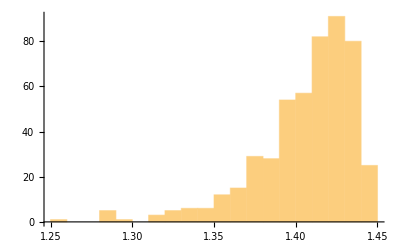

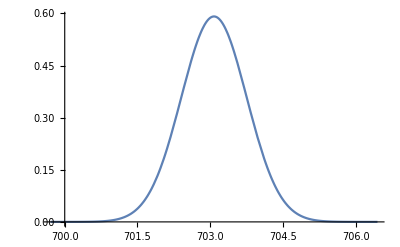

```mathematica
n=500;
samples=sortedData[[50501;;50500+n,2]]/10^38;
minmax=MinMax[samples]
{Mean[samples],Variance[samples],StandardDeviation[samples]}
{n Mean[samples],Sqrt[n Variance[samples]]}
Histogram[samples]

Plot[PDF[NormalDistribution[n Mean[samples],√(n Variance[samples])],X],{X,n Mean[samples]-5 √(n Variance[samples]),n Mean[samples]+5 √(n Variance[samples])},PlotRange->All]
```

```mathematica
sortedData[[50501,1]]
sortedData[[50500+n,1]]
```

1.00678×10^15

1.02302×10^15

```mathematica
1.0230169158086928*^15
```

1.02302×10^15

Sum of squared differences to mean given by Variance x (n-1) because mathematica returns unbiased estimator

```mathematica
Variance[samples](Length[samples]-1)
```

0.454037

```mathematica
Mean[{1,2}]
```

3/2

Update from conjugate prior to posterior

{500,1,1.40616,500,500,0.454037}

μ 1.40616 500 0.454037

-4102.132003549338123-1. λ-494.548/σSq+(703.08 μ)/σSq-(250. μ^2)/σSq+499 Log[λ]-(503 Log[σSq])/2

{10.5152,{λ→499.,μ→1.40616,σSq→0.000902659}}

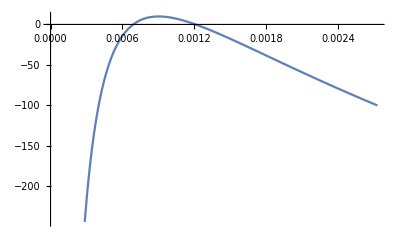

```mathematica
updateHyperpar[samples_,α0_,β0_,μ0_,n0_,ν0_,ν0σSq0_]:=Module[{xbar,n,sumsq},
xbar=Mean[samples];
n=Length[samples];
sumsq=(n-1)Variance[samples];
{n+α0,1+β0,(n0 μ0+n xbar)/(n0+n),n0+n,ν0+n,ν0σSq0+sumsq+(n0 n)/(n0+n)(μ0-xbar)^2}
]
updatePosterior[λ_,μ_,σSq_,samples_,a_]:=Module[{α0,β0=0,μ0=0,n0=0,ν0=0,ν0σSq0=0},
α0=1-a;
{α0,β0,μ0,n0,ν0,ν0σSq0}=updateHyperpar[samples,α0,β0,μ0,n0,ν0,ν0σSq0];
Print["μ ",μ0," ",ν0," ",ν0σSq0];
SimplifyLog[Log[Assuming[σSq>0&&λ>0&&n>0&&a≥0,PDF[NormalDistribution[μ0,√(σSq/n0)],μ] PDF[InverseGammaDistribution[ν0/2,ν0σSq0/2],σSq] 

(* β0 is a rate parameter but mathematica interprets 2nd arg as scale para *)PDF[GammaDistribution[α0, 1/β0],λ]//Simplify]]]//Expand
]
updateHyperpar[samples,0,0,0,0,0,0]
target=updatePosterior[λ,μ,σSq,samples,1]
(* Automatic optimization method fails to move but Newton works ok *)
FindMaximum[target,{{λ,Length[samples]-3.5},{μ,0.98Mean[samples]},{σSq, 0.99 Variance[samples]}},Method->"Newton"]
Plot[target/.{λ->1.05n,μ-> Mean[samples]},{σSq,0.00,3 0.0009098944933815481}]
```

```mathematica
PDF[NormalDistribution[μ0,√(σSq/n0)],μ] /.{μ0-> 1.4061594717404597,μ->1.4061594717404597, σSq-> 0.0009026587518831151,n0->n}//Log
PDF[InverseGammaDistribution[ν0/2,ν0σSq0/2],σSq] /.{σSq-> 0.0009026587518831151,ν0-> n, ν0σSq0-> 0.4540373521973925}//Log
```

5.69345

8.847142492819831

```mathematica
target/.{λ->496.5,μ->1.40615947174046,σSq->0.0009026587518831151}
```

10.5089

```mathematica
Mean[samples]
(n-1)/n Variance[samples]
```

1.40616

0.000908075

```mathematica
Log[PDF[GammaDistribution[n,1],n-1.]]
```

-4.02540858172609

```mathematica
Abs[-4.02540858172608950040940134903412834056`16.55939973831933]
```

4.02540858172609

## Moment generating function

```mathematica
(* LaplaceTransform of Gaussian gives a result but inverse does not *)
```

```mathematica
Assuming[λ>0&&σSq>0,LaplaceTransform[PDF[NormalDistribution[λ μ,√(λ σSq)],X],X,t]//Simplify]
```

1/2 ⅇ^(1/2 t λ (-2 μ+t σSq)) (1+Erf[(λ (μ-t σSq))/(√2 √(λ σSq))])

```mathematica
f[t_]:=1/2 ⅇ^(1/2 t λ (-2 μ+t σSq)) (1+Erf[(λ (μ-t σSq))/(√2 √(λ σSq))])
```

```mathematica
-D[f[t],t]/.t->0
%//PowerExpand
Assuming[λ>0&&σSq>0,PowerExpand[D[f[t],{t,2}]/.t->0]//Simplify]
-D[f[t],{t,3}]/.t->0//PowerExpand//FullSimplify
D[f[t],{t,4}]/.t->0//PowerExpand//FullSimplify
```

(ⅇ^(-(λ μ^2)/(2 σSq)) λ σSq)/(√(2 π) √(λ σSq))+1/2 λ μ (1+Erf[(λ μ)/(√2 √(λ σSq))])

(ⅇ^(-(λ μ^2)/(2 σSq)) √λ √σSq)/(√(2 π))+1/2 λ μ (1+Erf[(√λ μ)/(√2 √σSq)])

1/2 (ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) μ √(λ^3 σSq)+λ (λ μ^2+σSq) (1+Erf[(μ √(λ/σSq))/(√2)]))

(ⅇ^(-(λ μ^2)/(2 σSq)) λ^(3/2) √σSq (λ μ^2+2 σSq))/(√(2 π))+1/2 λ^2 μ (λ μ^2+3 σSq) (1+Erf[(√λ μ)/(√2 √σSq)])

(ⅇ^(-(λ μ^2)/(2 σSq)) λ^(5/2) μ √σSq (λ μ^2+5 σSq))/(√(2 π))+1/2 λ^2 (λ^2 μ^4+6 λ μ^2 σSq+3 σSq^2) (1+Erf[(√λ μ)/(√2 √σSq)])

```mathematica
(x-μ)^4//Expand
```

x^4-4 x^3 μ+6 x^2 μ^2-4 x μ^3+μ^4

```mathematica
Moment[NormalDistribution[μ, σ],3]
```

μ (μ^2+3 σ^2)

```mathematica
Assuming[a>0&&a∈Reals,a/√(a b)//Simplify]
FullSimplify[a/√(a b),Assumptions->Element[a,Reals]]
PowerExpand[a/√(a b)]
```

a/(√(a b))

a/(√(a b))

(√a)/(√b)

```mathematica
target
FindMaximum[target,{{λ,Length[samples]-12.1},{μ,0.98Mean[samples]},{σSq, 0.95 Variance[samples]}},Method->"Newton"]
```

-4102.132003549338123-1. λ-494.548/σSq+(703.08 μ)/σSq-(250. μ^2)/σSq+499 Log[λ]-(503 Log[σSq])/2

{10.5152,{λ→499.,μ→1.40616,σSq→0.000902659}}

μ and σ unchanged but λ increases by one integer unit

```mathematica
{max1, sol1}=FindMaximum[target+ Log[-D[f[t],t]/.t->0],{{λ,Length[samples]-12.1},{μ,0.98Mean[samples]},{σSq, 0.95 Variance[samples]}},Method->"Newton"]
```

FindMaximum::nrnum: The function value 218.596-Log[672.344 res Optim.minimizer] is not a real number at {λ,μ,σSq} = {487.9,1.37804,0.0008644}.

Set::shape: Lists {max1,sol1} and FindMaximum[target+Log[-∂_t f[t]/.t→0],{{λ,Length[samples]-12.1},{μ,0.98 Mean[samples]},{σSq,0.95 Variance[samples]}},Method→Newton] are not the same shape.

FindMaximum::nrnum: The function value 218.596-Log[672.344 res Optim.minimizer] is not a real number at {λ,μ,σSq} = {487.9,1.37804,0.0008644}.

FindMaximum[target+Log[-∂_t f[t]/.t→0],{{λ,Length[samples]-12.1},{μ,0.98 Mean[samples]},{σSq,0.95 Variance[samples]}},Method→Newton]

μ and σ unchanged but λ increases by two integer units

```mathematica
{max2, sol2}=FindMaximum[target +Log[D[f[t],{t,2}]/.t->0],{{λ,Length[samples]+0.3},{μ,1.01Mean[samples]},{σSq, 0.99 Variance[samples]}},Method->"Newton",StepMonitor:>Print["λ=",λ,", μ=",μ,",σ^2=",σSq]]
```

FindMaximum::nrnum: The function value 44.3631-Log[504863. res Optim.minimizer] is not a real number at {λ,μ,σSq} = {500.3,1.42022,0.000900796}.

Set::shape: Lists {max2,sol2} and FindMaximum[target+Log[∂_{t,2} f[t]/.t→0],{{λ,Length[samples]+0.3},{μ,1.01 Mean[samples]},{σSq,0.99 Variance[samples]}},Method→Newton,StepMonitor:>Print[λ=,λ,, μ=,μ,,σ^2=,σSq]] are not the same shape.

FindMaximum::nrnum: The function value 44.3631-Log[504863. res Optim.minimizer] is not a real number at {λ,μ,σSq} = {500.3,1.42022,0.000900796}.

FindMaximum[target+Log[∂_{t,2} f[t]/.t→0],{{λ,Length[samples]+0.3},{μ,1.01 Mean[samples]},{σSq,0.99 Variance[samples]}},Method→Newton,StepMonitor:>Print[λ=,λ,, μ=,μ,,σ^2=,σSq]]

Plot

```mathematica
ContourPlot[Exp[target +Log[D[f[t],{t,2}]/.t->0.]/.λ->n],{μ,1.39, 1.43},{σSq,0.0005, 0.0025}]
```

-Graphics-

```mathematica
Laplace[logf_,hessian_]:=Length[hessian]/2Log[2 π] +logf-1/2Log[Det[hessian]]
```

```mathematica
hessian1[λ_,μ_,σSq_]:=-D[target,{{λ,μ,σSq},2}]-D[Log[-D[f[t],t]/.t->0],{{λ,μ,σSq},2}]
hessian2[λ_,μ_,σSq_]:=-D[target,{{λ,μ,σSq},2}]-D[Log[D[f[t],{t,2}]/.t->0],{{λ,μ,σSq},2}]
```

```mathematica
hessian1[λ,μ,σSqsol1];
```

```mathematica
Print["mean from Laplace approx"];Laplace[max1,hessian1[λ,μ,σSq]/.sol1]//Exp
Print["std. dev. from Laplace approx."];
Exp[Laplace[max2,hessian2[λ,μ,σSq]/.sol2]]
Sqrt[%-(%%%^2)]
```

mean from Laplace approx

ReplaceAll::reps: {sol1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 ⅇ^max1 π)/(√Det[{{499/λ^2+(-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq^3 Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res σSq^2 Optim.minimizer)/(√(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res μ^2 Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^4 Optim.minimizer)/(4 √(2 π) σSq √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ ((3 λ μ σSq^2)/(4 √2 (λ σSq)^(5/2))-(μ σSq)/(√2 (λ σSq)^(3/2))) Optim.minimizer)/(√π)+(2 ⅇ^(-(λ μ^2)/(2 σSq)) res μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^3 (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(2 √π σSq))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),(res λ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/(2 ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2)-((ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (-(λ σSq)/(2 √2 (λ σSq)^(3/2))+1/(√2 √(λ σSq))) Optim.minimizer)/(√π)+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π σSq)+1/2 res Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),((-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq^2 Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res Optim.minimizer)/(√(2 π) √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^4 Optim.minimizer)/(4 √(2 π) σSq^2 √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ ((3 λ^2 μ σSq)/(4 √2 (λ σSq)^(5/2))-(λ μ)/(√2 (λ σSq)^(3/2))) Optim.minimizer)/(√π)+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(2 √π σSq^2))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))},{(res λ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/(2 ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2)-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))-(res Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/(2 ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))),500./σSq+(res^2 λ^2 (Optim.minimizer)^2 (1+Erf[(λ μ)/(√2 √(λ σSq))])^2)/(4 ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2)-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 Optim.minimizer)/(√(2 π) √(λ σSq) ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))),703.08/σSq^2-(500. μ)/σSq^2+(res λ Optim.minimizer (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))) (1+Erf[(λ μ)/(√2 √(λ σSq))]))/(2 ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2)+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2) ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))},{((-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 σSq Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))+(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq^2 Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^4 Optim.minimizer)/(4 √(2 π) σSq (λ σSq)^(3/2))-(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res Optim.minimizer)/(√(2 π) √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^4 Optim.minimizer)/(4 √(2 π) σSq^2 √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq)))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),703.08/σSq^2-(500. μ)/σSq^2+(res λ Optim.minimizer (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))) (1+Erf[(λ μ)/(√2 √(λ σSq))]))/(2 ((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2)-(-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^3 Optim.minimizer)/(2 √(2 π) σSq (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^3 Optim.minimizer)/(2 √(2 π) σSq^2 √(λ σSq)))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),989.096/σSq^3-(1406.16 μ)/σSq^3+(500. μ^2)/σSq^3-503/(2 σSq^2)+(-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq)))^2/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^2 Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))+(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 σSq Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 Optim.minimizer)/(√(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^4 Optim.minimizer)/(4 √(2 π) σSq^2 (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) σSq (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^4 Optim.minimizer)/(4 √(2 π) σSq^3 √(λ σSq)))/((ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))}}/.sol1])

std. dev. from Laplace approx.

ReplaceAll::reps: {sol2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 ⅇ^max2 π)/(√Det[{{499/λ^2+(-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res (2 λ μ^2+σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq^3 Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ σSq^2 Optim.minimizer)/(λ σSq)^(3/2)-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ^3 Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^5 Optim.minimizer)/(4 √(2 π) σSq √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res μ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) ((3 λ μ σSq^2)/(4 √2 (λ σSq)^(5/2))-(μ σSq)/(√2 (λ σSq)^(3/2))) Optim.minimizer)/(√π)+(2 ⅇ^(-(λ μ^2)/(2 σSq)) res (2 λ μ^2+σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)-(ⅇ^(-(λ μ^2)/(2 σSq)) res μ^2 (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(2 √π σSq)+res μ^2 Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),((-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^3 μ^2 Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) √(λ σSq))+res λ^2 μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res (2 λ μ^2+σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ^2 Optim.minimizer)/(√(λ σSq))-(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^4 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (2 λ μ^2+σSq) Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) (-(λ σSq)/(2 √2 (λ σSq)^(3/2))+1/(√2 √(λ σSq))) Optim.minimizer)/(√π)+(2 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π σSq)+2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),((-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^3 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+1/2 res λ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res (2 λ μ^2+σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ σSq^2 Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(λ σSq)^(3/2)+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^5 Optim.minimizer)/(4 √(2 π) σSq^2 √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(√(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (2 λ μ^2+σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) ((3 λ^2 μ σSq)/(4 √2 (λ σSq)^(5/2))-(λ μ)/(√2 (λ σSq)^(3/2))) Optim.minimizer)/(√π)+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(2 √π σSq^2)+1/2 res Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))},{((-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^3 μ^2 Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) √(λ σSq))+res λ^2 μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res (2 λ μ^2+σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(3 ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ^2 Optim.minimizer)/(√(λ σSq))+(5 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^4 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (2 λ μ^2+σSq) Optim.minimizer)/(√(2 π) √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ^2 (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))+(2 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),500./σSq+(-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^3 μ^2 Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) √(λ σSq))+res λ^2 μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^4 μ^3 Optim.minimizer)/(σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^3 Optim.minimizer)/(√(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) σSq √(λ σSq))+res λ^2 Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),703.08/σSq^2-(500. μ)/σSq^2+((-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^3 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+1/2 res λ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])) (-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^3 μ^2 Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) √(λ σSq))+res λ^2 μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-(-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^4 Optim.minimizer)/(2 √(2 π) σSq^2 √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^2 (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) σSq^2 √(λ σSq)))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))},{((-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^3 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+1/2 res λ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])) (-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(2 √(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ σSq Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res (λ^2 μ^2+λ σSq) (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res (2 λ μ^2+σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ σSq^2 Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(λ σSq)^(3/2)+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ μ Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^5 Optim.minimizer)/(4 √(2 π) σSq^2 √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 Optim.minimizer)/(√(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (2 λ μ^2+σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq (λ^2 μ^2+λ σSq) Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ^3 (λ^2 μ^2+λ σSq) Optim.minimizer)/(4 √(2 π) σSq (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))+μ/(√2 √(λ σSq))) Optim.minimizer)/(√π)+1/2 res Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),703.08/σSq^2-(500. μ)/σSq^2+((-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^3 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+1/2 res λ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])) (-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^3 μ^2 Optim.minimizer)/(√(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 σSq Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ (λ^2 μ^2+λ σSq) Optim.minimizer)/(√(2 π) √(λ σSq))+res λ^2 μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-(-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^2 Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^4 Optim.minimizer)/(2 √(2 π) σSq^2 √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^3 μ^2 Optim.minimizer)/(σSq √(λ σSq))+(5 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^2 (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) σSq (λ σSq)^(3/2)))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])),989.096/σSq^3-(1406.16 μ)/σSq^3+(500. μ^2)/σSq^3-503/(2 σSq^2)+(-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ σSq Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ Optim.minimizer)/(√(2 π) √(λ σSq))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^3 Optim.minimizer)/(2 √(2 π) σSq √(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(2 √(2 π) (λ σSq)^(3/2))+1/2 res λ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))^2-((3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ σSq Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^3 μ Optim.minimizer)/(λ σSq)^(3/2)-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^3 Optim.minimizer)/(2 √(2 π) σSq (λ σSq)^(3/2))+(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^4 μ^5 Optim.minimizer)/(4 √(2 π) σSq^3 √(λ σSq))+(3 ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ (λ^2 μ^2+λ σSq) Optim.minimizer)/(4 √(2 π) (λ σSq)^(5/2))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^3 μ^3 (λ^2 μ^2+λ σSq) Optim.minimizer)/(4 √(2 π) σSq^2 (λ σSq)^(3/2)))/((ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))]))}}/.sol2])

√(-(4 ⅇ^(2 max1) π^2)/Det[{1}/.sol1]+(2 ⅇ^max2 π)/(√Det[{1}/.sol2]))
 |  |  |  |

```mathematica
Print["mean from numerical integration"];NIntegrate[Exp[target] (-D[f[t],{t,1}]/.t->0),{λ,n-3 √n,n+3 √n},{μ,1.2,1.6},{σSq,0,0.005}]
```

mean from numerical integration

NIntegrate::inumr: The integrand (ⅇ^(-4102.13200354934-1. λ-(«18»)/σSq+(«18» μ)/σSq-(250. μ^2)/σSq) «1» ((ⅇ^(-(λ «1»)/(2 «3»)) res «1»«1»σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res «2» «1» (1+Erf[(λ μ)/(«1»)])))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{500-30 √5,500+30 √5},{1.2,1.6},{0,0.005}}.

NIntegrate[Exp[target] (-∂_{t,1} f[t]/.t→0),{λ,n-3 √n,n+3 √n},{μ,1.2,1.6},{σSq,0,0.005}]

```mathematica
Print["std.dev from numerical integration"];
NIntegrate[Exp[target] (D[f[t],{t,2}]/.t->0),{λ,n-3 √n,n+3 √n},{μ,1.35,1.45},{σSq,10^-4,0.005},Method->"AdaptiveMonteCarlo"]
Sqrt[%-(%%%^2)]
```

std.dev from numerical integration

NIntegrate::inumr: The integrand (ⅇ^(-4102.13200354934-1. λ-(«18»)/σSq+(«18» μ)/σSq-(250. μ^2)/σSq) λ^499 («1»))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate[Exp[target] (∂_{t,2} f[t]/.t→0),{λ,n-3 √n,n+3 √n},{μ,1.35,1.45},{σSq,1/10^4,0.005},Method→AdaptiveMonteCarlo]

NIntegrate::inumr: The integrand (ⅇ^(-4102.13200354934-1. λ-(«18»)/σSq+(«18» μ)/σSq-(250. μ^2)/σSq) λ^499 («1»))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1},{0,1}}.

NIntegrate::inumr: The integrand (ⅇ^(-4102.13200354934-1. λ-(«18»)/σSq+(«18» μ)/σSq-(250. μ^2)/σSq) «1» ((ⅇ^(-(λ «1»)/(2 «3»)) res «1»«1»σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res «2» «1» (1+Erf[(λ μ)/(«1»)])))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{500-30 √5,500+30 √5},{1.2,1.6},{0,0.005}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

√(-NIntegrate[Exp[target] (-∂_{t,1} f[t]/.t→0),{λ,n-3 √n,n+3 √n},{μ,1.2,1.6},{σSq,0,0.005}]^2+NIntegrate[Exp[target] (∂_{t,2} f[t]/.t→0),{λ,n-3 √n,n+3 √n},{μ,1.35,1.45},{σSq,1/10^4,0.005},Method→AdaptiveMonteCarlo])

Compare to plug-in estimates

```mathematica
Print["plug-in Mean"]; n Mean[samples]
Print["plug-in std. dev"]; Sqrt[n Variance[samples]]
```

plug-in Mean

703.08

plug-in std. dev

0.674498

And the observed value

```mathematica
Total[samples]
```

703.08

Wow, the plug-in estimate’s uncertainty is smaller by a factor of 100! How to explain this? From Poisson noise alone, a shift of X by √n μ=

```mathematica
Sqrt[n]Mean[samples]
```

31.4427

seems reasonable, that’s half of the total uncertainty that Laplace claims and exactly what numerical integration yields. If n fixed, shift the mean weight by how well it is constrained

```mathematica
n(Mean[samples]+√(Variance[samples]/n))
```

703.754

which happens to coincide with numerical integr. mean. Adding both numbers takes us to ~735, still quite far away from mean+std.dev

```mathematica
697.496290968137+69.83046678219846
```

767.327

but that doesn’t yet include the uncertainty about σ. Why is Laplace so different? Assuming the numerical integr. result is reliable, there could be a problem in the optimizer. They don’t move very much, and only Newton gives a result for initial values of the mean and variance that are very close to the sample mean and sample variance.

I should investigate how much can be done analytically. The integer results for λ seem promising.

## Assume mean and variance are fixed, only Poisson uncertainty

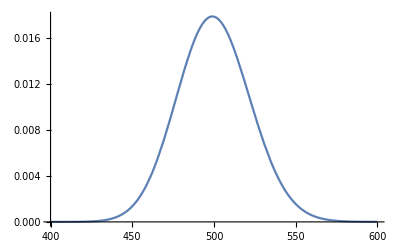

```mathematica
Plot[PDF[GammaDistribution[500,1],x],{x,400,600}]
```

```mathematica
target
```

-4102.132003549338123-1. λ-494.548/σSq+(703.08 μ)/σSq-(250. μ^2)/σSq+499 Log[λ]-(503 Log[σSq])/2

```mathematica
plugin={μ->Mean[samples],σSq->Variance[samples]}
```

{μ→1.40616,σSq→0.000909894}

```mathematica
D[f,λ]//Simplify
```

0

```mathematica
targetPoisson=Assuming[λ>0,Log[PDF[GammaDistribution[n, 1],λ]]//Simplify]//SimplifyLog;
{maxPoisson1, solPoisson1}=FindMaximum[targetPoisson +Log[-D[f[t],t]/.{t->0}/.plugin],{{λ,Length[samples]+3.3}},Method->"Newton"]
{maxPoisson2, solPoisson2}=FindMaximum[targetPoisson +Log[D[f[t],{t,2}]/.{t->0}/.plugin],{{λ,Length[samples]+3.3}},Method->"Newton"]
```

FindMaximum::nrnum: The function value 4.04383-Log[707.72 res Optim.minimizer] is not a real number at {λ} = {503.3}.

Set::shape: Lists {maxPoisson1,solPoisson1} and FindMaximum[targetPoisson+Log[-∂_t f[«1»]/.{t→0}/.plugin],{{λ,Length[samples]+3.3}},Method→Newton] are not the same shape.

FindMaximum::nrnum: The function value 4.04383-Log[707.72 res Optim.minimizer] is not a real number at {λ} = {503.3}.

FindMaximum[targetPoisson+Log[-∂_t f[t]/.{t→0}/.plugin],{{λ,Length[samples]+3.3}},Method→Newton]

FindMaximum::nrnum: The function value 4.04383-Log[500868. res Optim.minimizer] is not a real number at {λ} = {503.3}.

Set::shape: Lists {maxPoisson2,solPoisson2} and FindMaximum[targetPoisson+Log[∂_{t,2} f[t]/.{t→0}/.plugin],{{λ,Length[samples]+3.3}},Method→Newton] are not the same shape.

FindMaximum::nrnum: The function value 4.04383-Log[500868. res Optim.minimizer] is not a real number at {λ} = {503.3}.

FindMaximum[targetPoisson+Log[∂_{t,2} f[t]/.{t→0}/.plugin],{{λ,Length[samples]+3.3}},Method→Newton]

Find mode in λ: First and second moment integrands have mode shifted by one and two in numerical example. Can we derive this analytically?

```mathematica
400,600
```

```mathematica
tmp[λ_]:=targetPoisson +Log[-D[f[t],t]/.{t->0}/.plugin]//Simplify
tmp[λ]
Plot[tmp[λ],{λ,495, 505},PlotPoints->40]
```

-2605.47-λ+499 Log[λ]+Log[Optim.minimizer (0.0171159 ⅇ^(-1086.55 λ) res √λ+1. res λ+1. res λ Erf[32.9628 √λ])]

-Graphics-

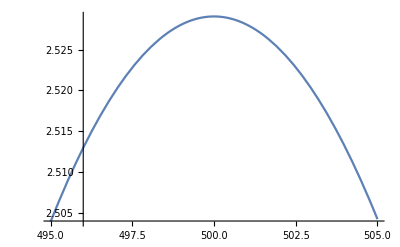
```mathematica
-Graphics-400,600
```

```mathematica
tmp=Assuming[λ>0,Log[PDF[GammaDistribution["n"-a+1, 1],λ]]//Simplify]//SimplifyLog
tmp2=tmp+Log[D[f[t],{t,2}]/.{t->0}]
tmp+=Log[-D[f[t],t]/.{t->0}]
(* to find the mode, set the derivative to zero, denominator irrelevant. But both denom and numerator are extremely large*)
D[tmp,λ]//TraditionalForm
%/.{"n"->n,a->1}/.plugin
(* the extra term due f(t) just approaches 1/λ for the numbers in our case. All terms with the exponential are strongly suppressed. *)
D[tmp2,λ]//TraditionalForm
%/.{"n"->n,a->1}/.plugin
Plot[tmp/.{"n"->n,a->1/2}/.{μ->0.97Mean[samples],σSq->1.283Variance[samples]},{λ,499,501}]
Clear[tmp,tmp2]
```

-λ+(n-a) Log[λ]-Log[Gamma[1+n-a]]

-λ+(n-a) Log[λ]+Log[(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) res λ^2 μ σSq Optim.minimizer)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) res λ^2 μ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res (λ^2 μ^2+λ σSq) Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])]-Log[Gamma[1+n-a]]

-λ+(n-a) Log[λ]+Log[(ⅇ^(-(λ μ^2)/(2 σSq)) res λ σSq Optim.minimizer)/(√(2 π) √(λ σSq))+1/2 res λ μ Optim.minimizer (1+Erf[(λ μ)/(√2 √(λ σSq))])]-Log[Gamma[1+n-a]]

(n-a)/λ+(1/2 μ res Optim.minimizer (erf((λ μ)/(√2 √(λ σSq)))+1)-(λ res σSq^2 Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(2 √(2 π) (λ σSq)^(3/2))-(λ μ^2 res Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(2 √(2 π) √(λ σSq))+(λ μ res Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)) (μ/(√2 √(λ σSq))-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))))/(√π)+(res σSq Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(√(2 π) √(λ σSq)))/(1/2 λ μ res Optim.minimizer (erf((λ μ)/(√2 √(λ σSq)))+1)+(λ res σSq Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(√(2 π) √(λ σSq)))-1

-1+499/λ+((0.00601694 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)-5.32907×10^-15 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res Optim.minimizer (1+Erf[32.9628 √λ]))/(0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ]))

(n-a)/λ+(1/2 res Optim.minimizer (2 λ μ^2+σSq) (erf((λ μ)/(√2 √(λ σSq)))+1)-(λ^2 μ res σSq^2 Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(2 √(2 π) (λ σSq)^(3/2))+(res Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)) (λ^2 μ^2+λ σSq) (μ/(√2 √(λ σSq))-(λ μ σSq)/(2 √2 (λ σSq)^(3/2))))/(√π)-(λ^2 μ^3 res Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(2 √(2 π) √(λ σSq))+(√(2/π) λ μ res σSq Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(√(λ σSq)))/(1/2 res Optim.minimizer (λ^2 μ^2+λ σSq) (erf((λ μ)/(√2 √(λ σSq)))+1)-(λ^2 μ res σSq Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(√(2 π) √(λ σSq))+(√(2/π) λ^2 μ res σSq Optim.minimizer ⅇ^(-(λ μ^2)/(2 σSq)))/(√(λ σSq)))-1

-1+499/λ+(0.0253823 ⅇ^(-1086.55 λ) res √λ Optim.minimizer-18.386 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+(9.29863 ⅇ^(-1086.55 λ) res (0.000909894 λ+1.97728 λ^2) Optim.minimizer)/(√λ)+1/2 res (0.000909894+3.95457 λ) Optim.minimizer (1+Erf[32.9628 √λ]))/(0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ]))

-Graphics-

```mathematica
1/2 (0.0009098944933815481+3.954568919930818 λ) (1+Erf[32.96279734104946 √λ])/(1/2 (0.0009098944933815481 λ+1.977284459965409 λ^2) (1+Erf[32.96279734104946 √λ]))
%/.λ-> 500
3.954568919930818/1.977284459965409
```

(0.000909894+3.95457 λ)/(0.000909894 λ+1.97728 λ^2)

0.004

2.

```mathematica
Erf[33. ]
Exp[-1086.55 500]
```

1.

4.627474251×10^-235942

The contribution ends up as 1/λ and 2/λ because σSq << λ μ^2, so all exponentials are zero at machine precision and the error function yield 1 with machine precisions.

```mathematica
Plot[Exp[targetPoisson +Log[-D[f[t],t]/.{t->0}/.plugin]],{λ,495, 505},PlotPoints->40]
```

-Graphics-

```mathematica
hessianPoisson1[λ_]:=-D[targetPoisson,{{λ},2}]-D[Log[-D[f[t],t]/.t->0],{{λ},2}]
hessianPoisson2[λ_]:=-D[targetPoisson,{{λ},2}]-D[Log[D[f[t],{t,2}]/.t->0],{{λ},2}]
```

```mathematica
Print["mean from Laplace"];Laplace[maxPoisson1,hessianPoisson1[λ]/.solPoisson1/.plugin]//Exp
Print["std. dev. from Laplace"];
Sqrt[Exp[Laplace[maxPoisson2,hessianPoisson2[λ]/.solPoisson2/.plugin]]-(%%^2)]
```

mean from Laplace

ReplaceAll::reps: {solPoisson1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 ⅇ^maxPoisson1 π)/(√Det[{{499/λ^2+((0.00601694 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)-5.32907×10^-15 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res Optim.minimizer (1+Erf[32.9628 √λ]))^2/(0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ]))^2-(-(0.00300847 ⅇ^(-1086.55 λ) res Optim.minimizer)/λ^(3/2)+(6.53768 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)+5.45697×10^-12 ⅇ^(-1086.55 λ) res √λ Optim.minimizer)/(0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ]))}}/.solPoisson1])

std. dev. from Laplace

ReplaceAll::reps: {solPoisson2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

√(-((4 ⅇ^(2 maxPoisson1) π^2)/Det[{{499/λ^2+((0.00601694 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)-5.32907×10^-15 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res Optim.minimizer (1+Erf[32.9628 √λ]))^2/(0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ]))^2-(-(0.00300847 ⅇ^(-1086.55 λ) res Optim.minimizer)/λ^(3/2)+(6.53768 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)+5.45697×10^-12 ⅇ^(-1086.55 λ) res √λ Optim.minimizer)/(0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ]))}}/.solPoisson1])+(2 ⅇ^maxPoisson2 π)/(√Det[{{499/λ^2+(0.0253823 ⅇ^(-1086.55 λ) res √λ Optim.minimizer-18.386 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+(9.29863 ⅇ^(-1086.55 λ) res (0.000909894 λ+1.97728 λ^2) Optim.minimizer)/(√λ)+1/2 res (0.000909894+3.95457 λ) Optim.minimizer (1+Erf[32.9628 √λ]))^2/(0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ]))^2-((0.0126912 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)-55.1581 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+19977.3 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+(18.5973 ⅇ^(-1086.55 λ) res (0.000909894+3.95457 λ) Optim.minimizer)/(√λ)-(4.64932 ⅇ^(-1086.55 λ) res (0.000909894 λ+1.97728 λ^2) Optim.minimizer)/λ^(3/2)-(10103.4 ⅇ^(-1086.55 λ) res (0.000909894 λ+1.97728 λ^2) Optim.minimizer)/(√λ)+1.97728 res Optim.minimizer (1+Erf[32.9628 √λ]))/(0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ]))}}/.solPoisson2]))

Verify Laplace with numerical integration. It seems to work, though the precision is only 10^-3 for the precision. But maybe it’s the numerical integration that’s off.

```mathematica
NIntegrate[(PDF[GammaDistribution[n,1],λ](-D[f[t],{t,1}]/.t->0)/.plugin),{λ,400,600}]
Exp[Laplace[maxPoisson2,hessianPoisson2[λ]/.solPoisson2/.plugin]]
NIntegrate[(PDF[GammaDistribution[n,1],λ](D[f[t],{t,2}]/.t->0)/.plugin),{λ,350,650}]
Sqrt[%-(Laplace[maxPoisson1,hessianPoisson1[λ]/.solPoisson1/.plugin]//Exp)^2]
```

NIntegrate::inumr: The integrand (0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ])) (Piecewise[{{(ⅇ^-λ λ^499)/(244027365198222013740247757084609385250714«1048»000000000000000000000000000000000000000000), λ>0}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{400,600}}.

NIntegrate[PDF[GammaDistribution[n,1],λ] (-∂_{t,1} f[t]/.t→0)/.plugin,{λ,400,600}]

ReplaceAll::reps: {solPoisson2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 ⅇ^maxPoisson2 π)/(√Det[{{499/λ^2+(0.0253823 ⅇ^(-1086.55 λ) res √λ Optim.minimizer-18.386 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+(9.29863 ⅇ^(-1086.55 λ) res (0.000909894 λ+1.97728 λ^2) Optim.minimizer)/(√λ)+1/2 res (0.000909894+3.95457 λ) Optim.minimizer (1+Erf[32.9628 √λ]))^2/(0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ]))^2-((0.0126912 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)-55.1581 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+19977.3 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+(18.5973 ⅇ^(-1086.55 λ) res (0.000909894+3.95457 λ) Optim.minimizer)/(√λ)-(4.64932 ⅇ^(-1086.55 λ) res (0.000909894 λ+1.97728 λ^2) Optim.minimizer)/λ^(3/2)-(10103.4 ⅇ^(-1086.55 λ) res (0.000909894 λ+1.97728 λ^2) Optim.minimizer)/(√λ)+1.97728 res Optim.minimizer (1+Erf[32.9628 √λ]))/(0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ]))}}/.solPoisson2])

NIntegrate::inumr: The integrand (0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ])) (Piecewise[{{(ⅇ^-λ λ^499)/(244027365198222013740247757084609«1065»0000000000000000000000000000000000), λ>0}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{350,650}}.

NIntegrate[PDF[GammaDistribution[n,1],λ] (∂_{t,2} f[t]/.t→0)/.plugin,{λ,350,650}]

NIntegrate::inumr: The integrand (0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ])) (Piecewise[{{(ⅇ^-λ λ^499)/(244027365198222013740247757084609«1065»0000000000000000000000000000000000), λ>0}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{350,650}}.

ReplaceAll::reps: {solPoisson1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand (0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ])) (Piecewise[{{(ⅇ^-λ λ^499)/(244027365198222013740247757084609«1065»0000000000000000000000000000000000), λ>0}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{350,650}}.

ReplaceAll::reps: {solPoisson1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand (0.0169216 ⅇ^(-1086.55 λ) res λ^(3/2) Optim.minimizer+1/2 res (0.000909894 λ+1.97728 λ^2) Optim.minimizer (1+Erf[32.9628 √λ])) (Piecewise[{{(ⅇ^-λ λ^499)/(244027365198222013740247757084609«1065»0000000000000000000000000000000000), λ>0}, {0, True}}]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{350,650}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

√(-((4 ⅇ^(2 maxPoisson1) π^2)/Det[{{499/λ^2+((0.00601694 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)-5.32907×10^-15 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res Optim.minimizer (1+Erf[32.9628 √λ]))^2/(0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ]))^2-(-(0.00300847 ⅇ^(-1086.55 λ) res Optim.minimizer)/λ^(3/2)+(6.53768 ⅇ^(-1086.55 λ) res Optim.minimizer)/(√λ)+5.45697×10^-12 ⅇ^(-1086.55 λ) res √λ Optim.minimizer)/(0.0120339 ⅇ^(-1086.55 λ) res √λ Optim.minimizer+0.70308 res λ Optim.minimizer (1+Erf[32.9628 √λ]))}}/.solPoisson1])+NIntegrate[PDF[GammaDistribution[n,1],λ] (∂_{t,2} f[t]/.t→0)/.plugin,{λ,350,650}])

Good agreement on the mean, less so on the standard dev. but that’s likely because a small error in NIntegrate gets exponentiated

```mathematica
702.962565693391/703.0688493193932
32.73321456883359/33.968265678321615
```

0.999849

0.963641

## Assume λ fixed, what’s the uncertainty due to μ and σ alone?

```mathematica
updatePosterior[μ_,σSq_,samples_,a_]:=Module[{α0,β0=0,μ0=0,n0=0,ν0=0,ν0σSq0=0},
α0=1-a;
{α0,β0,μ0,n0,ν0,ν0σSq0}=updateHyperpar[samples,α0,β0,μ0,n0,ν0,ν0σSq0];
Print[ν0," ",ν0σSq0];
SimplifyLog[Log[Assuming[σSq>0&&n>0&&a≥0,PDF[NormalDistribution[μ0,√(σSq/n0)],μ] PDF[InverseGammaDistribution[ν0/2,ν0σSq0/2],σSq] //Simplify]]]
]
targetμσSq=updatePosterior[μ,σSq,samples,1]
pluginλ={λ->n-1};
{maxμσSq1, solμσSq1}=FindMaximum[targetμσSq +Log[-D[f[t],t]/.{t->0}/.pluginλ],{{μ,0.98Mean[samples]},{σSq, 0.95 Variance[samples]}},Method->"Newton"]
{maxμσSq2, solμσSq2}=FindMaximum[targetμσSq +Log[D[f[t],{t,2}]/.{t->0}/.pluginλ],{{μ,0.98Mean[samples]},{σSq, 0.95 Variance[samples]}},Method->"Newton"]
```

500 0.454037

-1497.01615318760423+(-494.548+703.08 μ-250. μ^2)/σSq-(503 Log[σSq])/2

FindMaximum::nrnum: The function value 214.445-Log[687.64 res Optim.minimizer] is not a real number at {μ,σSq} = {1.37804,0.0008644}.

Set::shape: Lists {maxμσSq1,solμσSq1} and FindMaximum[targetμσSq+Log[-∂_t f[«1»]/.{t→0}/.pluginλ],{{μ,0.98 Mean[samples]},{σSq,0.95 Variance[samples]}},Method→Newton] are not the same shape.

FindMaximum::nrnum: The function value 214.445-Log[687.64 res Optim.minimizer] is not a real number at {μ,σSq} = {1.37804,0.0008644}.

FindMaximum[targetμσSq+Log[-∂_t f[t]/.{t→0}/.pluginλ],{{μ,0.98 Mean[samples]},{σSq,0.95 Variance[samples]}},Method→Newton]

FindMaximum::nrnum: The function value 214.445-Log[472849. res Optim.minimizer] is not a real number at {μ,σSq} = {1.37804,0.0008644}.

Set::shape: Lists {maxμσSq2,solμσSq2} and FindMaximum[targetμσSq+Log[∂_{t,2} f[t]/.{t→0}/.pluginλ],{{μ,0.98 Mean[samples]},{σSq,0.95 Variance[samples]}},Method→Newton] are not the same shape.

FindMaximum::nrnum: The function value 214.445-Log[472849. res Optim.minimizer] is not a real number at {μ,σSq} = {1.37804,0.0008644}.

FindMaximum[targetμσSq+Log[∂_{t,2} f[t]/.{t→0}/.pluginλ],{{μ,0.98 Mean[samples]},{σSq,0.95 Variance[samples]}},Method→Newton]

```mathematica
hessianμσSq1[μ_,σSq_]:=-D[targetμσSq-Log[-D[f[t],t]/.t->0],{{μ,σSq},2}]
hessianμσSq2[μ_,σSq_]:=-D[targetμσSq-Log[D[f[t],{t,2}]/.t->0],{{μ,σSq},2}]
```

```mathematica
Print["mean from Laplace"];Laplace[maxμσSq1,hessianμσSq1[μ,σSq]/.solμσSq1/.pluginλ]//Exp
Print["std. dev. from Laplace"];
Sqrt[Exp[Laplace[maxμσSq2,hessianμσSq2[λ]/.solμσSq2/.pluginλ]]-(%%^2)]
```

mean from Laplace

ReplaceAll::reps: {solμσSq1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 ⅇ^maxμσSq1 π)/(√Det[{{500./σSq-(249001 res^2 (Optim.minimizer)^2 (1+Erf[(√(499/2) μ)/(√σSq)])^2)/(4 (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)+(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res Optim.minimizer)/(√σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))),(703.08-500. μ)/σSq^2-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res^2 (Optim.minimizer)^2 (1+Erf[(√(499/2) μ)/(√σSq)]))/(4 √σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ Optim.minimizer)/(2 σSq^(3/2) (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)])))},{(703.08-500. μ)/σSq^2-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res^2 (Optim.minimizer)^2 (1+Erf[(√(499/2) μ)/(√σSq)]))/(4 √σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ Optim.minimizer)/(2 σSq^(3/2) (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))),-(2 (-494.548+703.08 μ-250. μ^2))/σSq^3-503/(2 σSq^2)-(499 ⅇ^(-(499 μ^2)/σSq) res^2 (Optim.minimizer)^2)/(8 π σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)+((499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ^2 Optim.minimizer)/(4 σSq^(5/2))-(ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res Optim.minimizer)/(4 σSq^(3/2)))/(ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))}}/.solμσSq1])

std. dev. from Laplace

ReplaceAll::reps: {solμσSq2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

√((2 ⅇ^maxμσSq2 π)/(√Det[hessianμσSq2[499]/.solμσSq2])-(4 ⅇ^(2 maxμσSq1) π^2)/Det[{{500./σSq-(249001 res^2 (Optim.minimizer)^2 (1+Erf[(√(499/2) μ)/(√σSq)])^2)/(4 (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)+(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res Optim.minimizer)/(√σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))),(703.08-500. μ)/σSq^2-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res^2 (Optim.minimizer)^2 (1+Erf[(√(499/2) μ)/(√σSq)]))/(4 √σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ Optim.minimizer)/(2 σSq^(3/2) (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)])))},{(703.08-500. μ)/σSq^2-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res^2 (Optim.minimizer)^2 (1+Erf[(√(499/2) μ)/(√σSq)]))/(4 √σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)-(499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ Optim.minimizer)/(2 σSq^(3/2) (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))),-(2 (-494.548+703.08 μ-250. μ^2))/σSq^3-503/(2 σSq^2)-(499 ⅇ^(-(499 μ^2)/σSq) res^2 (Optim.minimizer)^2)/(8 π σSq (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))^2)+((499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ^2 Optim.minimizer)/(4 σSq^(5/2))-(ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res Optim.minimizer)/(4 σSq^(3/2)))/(ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)]))}}/.solμσSq1])

Adding the variance in quadrature matches very well with the above 3D result: so the main source of uncertainty is due to μ and σ^2 and not due to the Poisson noise in λ!

```mathematica
√(61.642679544896204^2+32.7^2)
```

69.779

Verify Laplace with numerical integration. It seems to work, though the precision is only 10^-3 for the precision. But maybe it’s the numerical integration that’s off.

```mathematica
NIntegrate[(Exp[targetμσSq ](-D[f[t],{t,1}]/.t->0)/.pluginλ),{μ,1.3,1.5},{σSq,0.0002,0.004}]
Exp[Laplace[maxμσSq2,hessianμσSq2[λ]/.solμσSq2/.pluginλ]]
NIntegrate[(Exp[targetμσSq ](D[f[t],{t,2}]/.t->0)/.pluginλ),{μ,1.3,1.5},{σSq,0.0002,0.004}]
Sqrt[%-(Laplace[maxμσSq1,hessianμσSq1[λ]/.solμσSq1/.pluginλ]//Exp)^2]
```

NIntegrate::inumr: The integrand (ⅇ^(-1497.0161531876+(«1»)/σSq) (ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res √σSq Optim.minimizer+499/2 res μ Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)])))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.3,1.5},{0.0002,0.004}}.

NIntegrate[Exp[targetμσSq] (-∂_{t,1} f[t]/.t→0)/.pluginλ,{μ,1.3,1.5},{σSq,0.0002,0.004}]

ReplaceAll::reps: {solμσSq2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(2 ⅇ^maxμσSq2 π)/(√Det[hessianμσSq2[499]/.solμσSq2])

NIntegrate::inumr: The integrand (ⅇ^(-1497.0161531876+(«1»)/σSq) (-499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ √σSq Optim.minimizer+«1»+1/2 res (249001 «1»+«1») Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)])))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.3,1.5},{0.0002,0.004}}.

NIntegrate[Exp[targetμσSq] (∂_{t,2} f[t]/.t→0)/.pluginλ,{μ,1.3,1.5},{σSq,0.0002,0.004}]

NIntegrate::inumr: The integrand (ⅇ^(-1497.0161531876+(«1»)/σSq) (-499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ √σSq Optim.minimizer+«1»+1/2 res (249001 «1»+«1») Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)])))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.3,1.5},{0.0002,0.004}}.

ReplaceAll::reps: {solμσSq1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand (ⅇ^(-1497.0161531876+(«1»)/σSq) (-499 ⅇ^(-(499 μ^2)/(2 σSq)) √(499/(2 π)) res μ √σSq Optim.minimizer+«1»+1/2 res (249001 «1»+«1») Optim.minimizer (1+Erf[(√(499/2) μ)/(√σSq)])))/σSq^(503/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.3,1.5},{0.0002,0.004}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

√(-(4 ⅇ^(2 maxμσSq1) π^2)/Det[hessianμσSq1[499]/.solμσSq1]+NIntegrate[Exp[targetμσSq] (∂_{t,2} f[t]/.t→0)/.pluginλ,{μ,1.3,1.5},{σSq,0.0002,0.004}])

```mathematica
DensityPlot[(Exp[targetμσSq ](-D[f[t],{t,1}]/.t->0)/.pluginλ),{μ,1.39,1.42},{σSq,0.0002,0.0015},PlotLegends->Automatic,ColorFunction->GrayLevel]
```

-Graphics-

## Marginal distributions of μ and σSq

Marginal P(σSq) is just the conditional of the model, InverseGamma

Mean 0.000911647

std. dev. 0.0000578896

rel. unc. 0.0635001

mode 0.000904382

sample variance 0.000909894

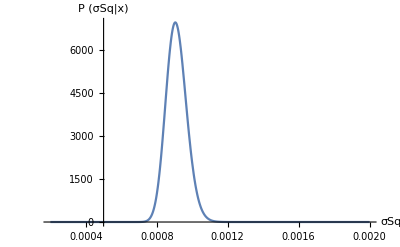

```mathematica
tmp=InverseGammaDistribution[ν0/2,ν0σSq0/2]/.{ν0->500,ν0σSq0-> 0.454};
Print["Mean ",Mean[tmp]]
Print["std. dev. ",StandardDeviation[tmp]]
Print["rel. unc. ", StandardDeviation[tmp]/Mean[tmp]]
Print["mode ",ν0σSq0/2/(ν0/2+1)/.{ν0->500,ν0σSq0-> 0.454}]
Print["sample variance ",Variance[samples]]
Plot[PDF[tmp,σSq],{σSq,0.0002,0.002},PlotRange->Full,AxesLabel->{σSq,P(σSq | x)}]
```

Marginal of μ is a t distribution but because we have lots of observations, it can be well approx. by Gaussian around sample mean with a tiny width of less than 0.1 %

0.001349

0.000959347

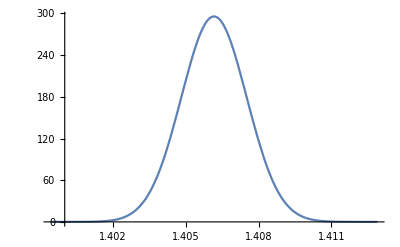

```mathematica
tmp=StandardDeviation[samples]/√n
tmp2=Mean[samples];
tmp/tmp2
Plot[PDF[NormalDistribution[Mean[samples],tmp],μ],{μ,tmp2-5 tmp,tmp2+5tmp}]
```

Transforming to standard deviation reduces the relative uncertainty by a factor of 2

TransformedDistribution[√x,x\[Distributed]InverseGammaDistribution[250,0.227]]

0.000956477

0.0301783

0.0316942

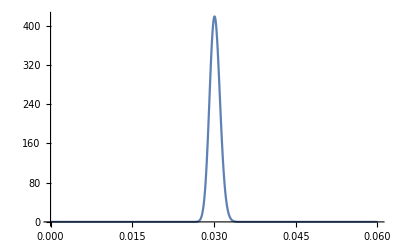

```mathematica
tmp=TransformedDistribution[√σSq,σSq\[Distributed](InverseGammaDistribution[ν0/2,ν0σSq0/2]/.{ν0->500,ν0σSq0-> 0.454})]
StandardDeviation[tmp]
Mean[tmp]
%%/%
Plot[PDF[tmp,x],{x,0,0.06},PlotRange->Full]
```

No idea why this does not work, same as above with Normal instead of InverseGamma

```mathematica
tmp=TransformedDistribution[√y,y\[Distributed]NormalDistribution[0.94,0.057889]]
Mean[tmp]
Plot[PDF[tmp,x],{x,0,1}]
```

TransformedDistribution[√x,x\[Distributed]NormalDistribution[0.94,0.057889]]

Mean[TransformedDistribution[√x,x\[Distributed]NormalDistribution[0.94,0.057889]]]

$Aborted